# Progetto Fondamenti di Automatica - Mariaida Perri mat. 239943 Esercizio a: Sistema LTI-TC

Inseriamo i parametri del sistema

```mathematica
ClearAll["Global`*"]
```

```mathematica
A = {{0, 4/225, 59/75, -76/225}, 
     {1, 221/225, -134/75, 301/225}, 
     {2, 446/225, -134/75, 301/225}, 
     {1, 221/225, -59/75, -149/225}}
```

{{0,4/225,59/75,-76/225},{1,221/225,-134/75,301/225},{2,446/225,-134/75,301/225},{1,221/225,-59/75,-149/225}}

```mathematica
A // MatrixForm
```

(0 | 4/225 | 59/75 | -76/225
1 | 221/225 | -134/75 | 301/225
2 | 446/225 | -134/75 | 301/225
1 | 221/225 | -59/75 | -149/225)

```mathematica
B = {{1},{-1},{-1},{-1}}
```

{{1},{-1},{-1},{-1}}

```mathematica
B//MatrixForm
```

(1
-1
-1
-1)

Chiamiamo C1 la matrice C, poichè il carattere C in Mathematica è un carattere riservato

```mathematica
C1 = {{2, 8, -6, 0}}
```

{{2,8,-6,0}}

```mathematica
C1 // MatrixForm
```

(2 | 8 | -6 | 0)

1. Modi naturali del sistema
Determiniamo lo spettro di A

```mathematica
P[λ_] := CharacteristicPolynomial[A,λ]
P[λ]
```

4/225+(44 λ)/225+(181 λ^2)/225+(22 λ^3)/15+λ^4

```mathematica
Solve[P[λ] == 0, λ]
```

{{λ→-2/5},{λ→-2/5},{λ→-1/3},{λ→-1/3}}

Controlliamo la correttezza dei risultati ottenuti, utilizzando un’apposita funzione di Mathematica

```mathematica
Eigenvalues[A]
```

{-2/5,-2/5,-1/3,-1/3}

Calcolo il polinomio minimo

```mathematica
MatrixMinimalPolynomial[a_List?MatrixQ,x_] := Module[{i,n=1,qu={},mnm={Flatten[IdentityMatrix[Length[a]]]}},
While[Length[qu]==0,AppendTo[mnm,Flatten[MatrixPower[a,n]]];
qu=NullSpace[Transpose[mnm]];
n++];
First[qu].Table[x^i,{i,0,n-1}]]
```

```mathematica
MatrixMinimalPolynomial[A,x]
```

4/225+(44 x)/225+(181 x^2)/225+(22 x^3)/15+x^4

```mathematica
Factor[MatrixMinimalPolynomial[A,x]]
```

1/225 (1+3 x)^2 (2+5 x)^2

```mathematica
CharacteristicPolynomial[A,x]
```

4/225+(44 x)/225+(181 x^2)/225+(22 x^3)/15+x^4

```mathematica
Factor[CharacteristicPolynomial[A,x]]
```

1/225 (1+3 x)^2 (2+5 x)^2

Il polinomio minimo e il polinomio caratteristico coincidono, ma sia (1+3x), sia (2+5x), legati ai due autovalori multipli, non hanno grado unitario, di conseguenza la matrice A non è diagonalizzabile.
Equivalentemente, si può ottenere questo risultato calcolando molteplicità algebrica e geometrica.

```mathematica
NullSpace[A-(-2/5) IdentityMatrix[4]]
```

{{137/8,-187/8,-31/4,1}}

```mathematica
NullSpace[A-(-1/3) IdentityMatrix[4]]
```

{{29,-38,-11,1}}

Poichè la molteplicità geometrica di entrambi gli autovalori multipli è pari ad uno, mentre la loro molteplicità algebrica è due, ancora una volta abbiamo la conferma del fatto che la matrice A non sia diagonalizzabile. 
Pertanto dobbiamo ricorrere alla forma di Jordan.

```mathematica
{T, Λ} = JordanDecomposition[A]
```

{{{137/8,1975/16,29,252},{-187/8,-2475/16,-38,-306},{-31/4,-75/2,-11,-63},{1,0,1,0}},{{-2/5,1,0,0},{0,-2/5,0,0},{0,0,-1/3,1},{0,0,0,-1/3}}}

```mathematica
Λ // MatrixForm
```

(-2/5 | 1 | 0 | 0
0 | -2/5 | 0 | 0
0 | 0 | -1/3 | 1
0 | 0 | 0 | -1/3)

A questo punto, bisogna calcolare l'esponenziale di matrice della forma canonica di Jordan di A per visualizzare i modi naturali.

```mathematica
Simplify[MatrixExp[Λ t]] // MatrixForm
```

(ⅇ^(-2 t/5) | ⅇ^(-2 t/5) t | 0 | 0
0 | ⅇ^(-2 t/5) | 0 | 0
0 | 0 | ⅇ^(-t/3) | ⅇ^(-t/3) t
0 | 0 | 0 | ⅇ^(-t/3))

Stampiamo il grafico dei modi polinomial-esponenziali

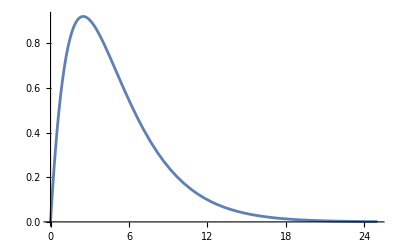

```mathematica
Plot[t Exp[-2/5 t], {t, 0, 25}, PlotRange -> All]
```

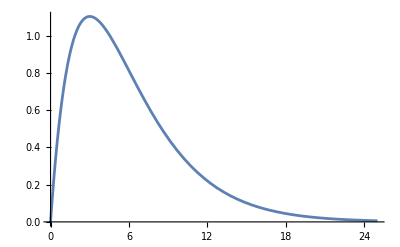

```mathematica
Plot[t Exp[-1/3 t], {t,0,25}, PlotRange->All]
```

Grafico dei modi naturali

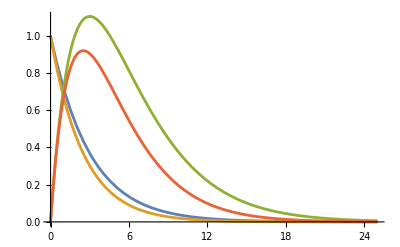

```mathematica
Plot[{Exp[-1/3 t], Exp[-2/5t], t Exp[-1/3 t], t Exp[-2/5 t]}, {t,0,25}, PlotRange->All]
```

2. Risposta libera dato uno stato iniziale x_0
Riprendiamo le precedenti matrici T e Λ

```mathematica
Λ // MatrixForm
```

(-2/5 | 1 | 0 | 0
0 | -2/5 | 0 | 0
0 | 0 | -1/3 | 1
0 | 0 | 0 | -1/3)

```mathematica
T // MatrixForm
```

(137/8 | 1975/16 | 29 | 252
-187/8 | -2475/16 | -38 | -306
-31/4 | -75/2 | -11 | -63
1 | 0 | 1 | 0)

Inseriamo lo stato inziale x_0

```mathematica
Subscript[x, 0]= {{2},{2},{1},{-3}}
```

{{2},{2},{1},{-3}}

```mathematica
Subscript[x, 0] // MatrixForm
```

(2
2
1
-3)

Proiettiamo lo stato iniziale lungo le colonne di T

```mathematica
Subscript[z, 0] = Inverse[T].Subscript[x, 0]
```

{{1484},{1608/25},{-1487},{349/9}}

```mathematica
Subscript[z, 0] // MatrixForm
```

(1484
1608/25
-1487
349/9)

Otteniamo la risposta libera nello stato

```mathematica
Subscript[x, l][t_] := T.MatrixExp[Λ t].Subscript[z, 0]
Subscript[x, l][t] // MatrixForm
```

(50827/2 ⅇ^(-2 t/5)-43123 ⅇ^(-t/3)+1608/25 (1975/16 ⅇ^(-2 t/5)+137/8 ⅇ^(-2 t/5) t)+349/9 (252 ⅇ^(-t/3)+29 ⅇ^(-t/3) t)
-69377/2 ⅇ^(-2 t/5)+56506 ⅇ^(-t/3)+1608/25 (-2475/16 ⅇ^(-2 t/5)-187/8 ⅇ^(-2 t/5) t)+349/9 (-306 ⅇ^(-t/3)-38 ⅇ^(-t/3) t)
-11501 ⅇ^(-2 t/5)+16357 ⅇ^(-t/3)+1608/25 (-75/2 ⅇ^(-2 t/5)-31/4 ⅇ^(-2 t/5) t)+349/9 (-63 ⅇ^(-t/3)-11 ⅇ^(-t/3) t)
1484 ⅇ^(-2 t/5)-1487 ⅇ^(-t/3)+1608/25 ⅇ^(-2 t/5) t+349/9 ⅇ^(-t/3) t)

Grafico della risposta libera nello stato

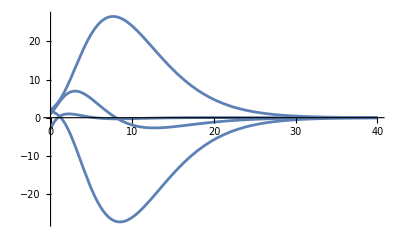

```mathematica
Plot[Subscript[x, l][t], {t,0,40}, PlotRange->All]
```

Risposta libera nell’uscita

```mathematica
C1 // MatrixForm
```

(2 | 8 | -6 | 0)

```mathematica
Subscript[y, l][t_] := C1.Subscript[x, l][t]
```

```mathematica
Expand[Subscript[y, l][t]]
```

{{-206920 ⅇ^(-2 t/5)+206934 ⅇ^(-t/3)-6834 ⅇ^(-2 t/5) t-6980 ⅇ^(-t/3) t}}

Grafico della risposta libera nell’uscita

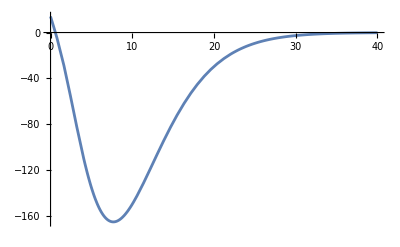

```mathematica
Plot[Subscript[y, l][t], {t,0,40},PlotRange->All]
```

3. Studio della configurazione degli stati iniziali che attivano sulla risposta libera alcuni modi naturali ed altri no

```mathematica
Λ//MatrixForm
```

(-2/5 | 1 | 0 | 0
0 | -2/5 | 0 | 0
0 | 0 | -1/3 | 1
0 | 0 | 0 | -1/3)

```mathematica
T//MatrixForm
```

(137/8 | 1975/16 | 29 | 252
-187/8 | -2475/16 | -38 | -306
-31/4 | -75/2 | -11 | -63
1 | 0 | 1 | 0)

```mathematica
Transpose[Eigenvectors[A]]//MatrixForm
```

(137/8 | 0 | 29 | 0
-187/8 | 0 | -38 | 0
-31/4 | 0 | -11 | 0
1 | 0 | 1 | 0)

Eseguiamo dei controlli sulle matrici A e T: verifichiamo che la prima e la terza colonna siano autovettori standard della matrice A e che la seconda e la quarta siano invece autovettori generalizzati

```mathematica
(A-(-2/5)IdentityMatrix[4]).T[[All,1]]
```

{0,0,0,0}

```mathematica
(A-(-1/3)IdentityMatrix[4]).T[[All,3]]
```

{0,0,0,0}

```mathematica
(A-(-2/5)IdentityMatrix[4]).T[[All,2]]
```

{137/8,-187/8,-31/4,1}

```mathematica
(A-(-1/3)IdentityMatrix[4]).T[[All,4]]
```

{29,-38,-11,1}

```mathematica
(A-(-2/5)IdentityMatrix[4]).(A-(-2/5)IdentityMatrix[4]).T[[All,2]]
```

{0,0,0,0}

```mathematica
(A-(-1/3)IdentityMatrix[4]).(A-(-1/3)IdentityMatrix[4]).T[[All,4]]
```

{0,0,0,0}

Stato iniziale allineato lungo la prima colonna di T

```mathematica
Subscript[x, 0] = T[[All,1]]
```

{137/8,-187/8,-31/4,1}

```mathematica
Subscript[z, 0]=Inverse[T].Subscript[x, 0]
```

{1,0,0,0}

```mathematica
Subscript[x, l][t_]:= T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Expand[Subscript[x, l][t]] // MatrixForm
```

(137/8 ⅇ^(-2 t/5)
-187/8 ⅇ^(-2 t/5)
-31/4 ⅇ^(-2 t/5)
ⅇ^(-2 t/5))

Stato iniziale allineato lungo la seconda colonna di T

```mathematica
Subscript[x, 0] = T[[All,2]]
```

{1975/16,-2475/16,-75/2,0}

```mathematica
Subscript[z, 0] = Inverse[T].Subscript[x, 0]
```

{0,1,0,0}

```mathematica
Subscript[x, l][t_] := T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Expand[Subscript[x, l][t]] // MatrixForm
```

(1975/16 ⅇ^(-2 t/5)+137/8 ⅇ^(-2 t/5) t
-2475/16 ⅇ^(-2 t/5)-187/8 ⅇ^(-2 t/5) t
-75/2 ⅇ^(-2 t/5)-31/4 ⅇ^(-2 t/5) t
ⅇ^(-2 t/5) t)

Stato iniziale allineato lungo la terza colonna di T

```mathematica
Subscript[x, 0] = T[[All,3]]
```

{29,-38,-11,1}

```mathematica
Subscript[z, 0] = Inverse[T].Subscript[x, 0]
```

{0,0,1,0}

```mathematica
Subscript[x, l][t_] := T.MatrixExp[Λ t].Subscript[z, 0]
Expand[Subscript[x, l][t]] // MatrixForm
```

(29 ⅇ^(-t/3)
-38 ⅇ^(-t/3)
-11 ⅇ^(-t/3)
ⅇ^(-t/3))

Stato iniziale allineato lungo la quarta colonna di T

```mathematica
Subscript[x, 0] = T[[All,4]]
```

{252,-306,-63,0}

```mathematica
Subscript[z, 0] = Inverse[T].Subscript[x, 0]
```

{0,0,0,1}

```mathematica
Subscript[x, l][t_] := T.MatrixExp[Λ t].Subscript[z, 0]
Expand[Subscript[x, l][t]] // MatrixForm
```

(252 ⅇ^(-t/3)+29 ⅇ^(-t/3) t
-306 ⅇ^(-t/3)-38 ⅇ^(-t/3) t
-63 ⅇ^(-t/3)-11 ⅇ^(-t/3) t
ⅇ^(-t/3) t)

Se volessimo “accendere” solo il modo ⅇ^(-2 t/5)  ed ⅇ^(-t/3):

```mathematica
Subscript[x, 0] = 3 T[[All,1]] + 2T[[All,3]]
```

{875/8,-1169/8,-181/4,5}

```mathematica
Subscript[z, 0] = Inverse[T].Subscript[x, 0]
```

{3,0,2,0}

```mathematica
Subscript[x, l][t_] := T.MatrixExp[Λ t].Subscript[z, 0]
```

```mathematica
Expand[Subscript[x, l][t]] // MatrixForm
```

(411/8 ⅇ^(-2 t/5)+58 ⅇ^(-t/3)
-561/8 ⅇ^(-2 t/5)-76 ⅇ^(-t/3)
-93/4 ⅇ^(-2 t/5)-22 ⅇ^(-t/3)
3 ⅇ^(-2 t/5)+2 ⅇ^(-t/3))

4. Funzione di trasferimento, poli e zeri

```mathematica
G[s_] := Simplify[C1.Inverse[s IdentityMatrix[4]-A].B]
```

```mathematica
G[s]
```

{{(450 (-3+s))/((2+11 s+15 s^2)^2)}}

```mathematica
CharacteristicPolynomial[A,s]
```

4/225+(44 s)/225+(181 s^2)/225+(22 s^3)/15+s^4

```mathematica
Eigenvalues[A]
```

{-2/5,-2/5,-1/3,-1/3}

Poli

```mathematica
Solve[Denominator[G[s][[1]]] == 0,s]
```

{{s→-2/5},{s→-2/5},{s→-1/3},{s→-1/3}}

Coincidono con gli autovalori di A

Zeri

```mathematica
Solve[Numerator[G[s][[1]]] == 0,s]
```

{{s→3}}

Utilizzando la funzione built-in di Mathematica:

```mathematica
Σ = StateSpaceModel[{A,B,C1}]
```

04/22559/75-76/22511221/225-134/75301/225-12446/225-134/75301/225-11221/225-59/75-149/225-128-600StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

```mathematica
FdT = Simplify[TransferFunctionModel[Σ]]
```

(450 (-3+s))/((2+11 s+15 s^2)^2)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s1145021FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Poli = TransferFunctionPoles[Σ]
```

{{{-2/5,-2/5,-1/3,-1/3}}}

```mathematica
Zeri = TransferFunctionZeros[Σ]
```

{{{3}}}

5. Risposta al gradino unitario e suo grafico

```mathematica
U[s_]:= LaplaceTransform[UnitStep[t],t,s]
U[s]
```

1/s

```mathematica
Y[s_] := G[s]×U[s]
Y[s]
```

{{(450 (-3+s))/(s (2+11 s+15 s^2)^2)}}

Scomposizione in fratti semplici

```mathematica
Subscript[Y, f][s_]:=Subscript[C, 1]/s + Subscript[C, 21]/(s+2/5)+ Subscript[C, 22]/(s+2/5)^2+ Subscript[C, 31]/(s+1/3)+Subscript[C, 32]/(s+1/3)^2
Subscript[Y, f][s]
```

C_1/s+C_21/(2/5+s)+C_22/(2/5+s)^2+C_31/(1/3+s)+C_32/(1/3+s)^2

Troviamo i coefficienti

```mathematica
Subscript[C, 1]= lim_(s->0) s G[s] 1/s
```

{{-675/2}}

```mathematica
Subscript[C, 1]=G[0]
```

{{-675/2}}

```mathematica
Subscript[C, 22]=1/((2-2)!)lim_(s->-2/5) ((s+2/5)^2 Y[s])
```

{{3825}}

```mathematica
Subscript[C, 21]=1/((2-1)!)lim_(s->-2/5) D[(s+2/5)^2 Y[s],s]
```

{{246375/2}}

```mathematica
Subscript[C, 32]=1/((2-2)!)lim_(s->-1/3) ((s+1/3)^2 Y[s])
```

{{4500}}

```mathematica
Subscript[C, 31]=1/((2-1)!)lim_(s->-1/3) D[(s+1/3)^2 Y[s],s]
```

{{-122850}}

```mathematica
Subscript[Y, f][s]
```

{{-675/(2 s)+4500/(1/3+s)^2-122850/(1/3+s)+3825/(2/5+s)^2+246375/(2 (2/5+s))}}

```mathematica
Apart[Y[s]]
```

{{-675/(2 s)+40500/(1+3 s)^2-368550/(1+3 s)+95625/(2+5 s)^2+1231875/(2 (2+5 s))}}

Seppur le due forme sembrino diverse, basta mettere in evidenza il 3 nel caso di 1/3 e il 5 nel caso di 2/5.

Passiamo al dominio del tempo

```mathematica
Subscript[yExp, f][t_]:=Subscript[C, 1] UnitStep[t]+Subscript[C, 21] Exp[-2/5 t]UnitStep[t]+Subscript[C, 22] t Exp[-2/5 t]UnitStep[t]+Subscript[C, 31] Exp[-1/3 t]UnitStep[t]+Subscript[C, 32] t Exp[-1/3 t]UnitStep[t]
Subscript[yExp, f][t]
```

{{-(675 UnitStep[t])/2+246375/2 ⅇ^(-2 t/5) UnitStep[t]-122850 ⅇ^(-t/3) UnitStep[t]+3825 ⅇ^(-2 t/5) t UnitStep[t]+4500 ⅇ^(-t/3) t UnitStep[t]}}

```mathematica
Expand[InverseLaplaceTransform[Y[s],s,t]]
```

{{-675/2+246375/2 ⅇ^(-2 t/5)-122850 ⅇ^(-t/3)+3825 ⅇ^(-2 t/5) t+4500 ⅇ^(-t/3) t}}

Risposta a regime

```mathematica
Subscript[Y, reg][t_]:= (-675 UnitStep[t])/2
```

```mathematica
Subscript[Y, reg][t]
```

-(675 UnitStep[t])/2

Risposta transitiva

```mathematica
Subscript[Y, tr][t_]:=Subscript[yExp, f][t]-Subscript[Y, reg][t]
```

```mathematica
Subscript[Y, tr][t]
```

{{246375/2 ⅇ^(-2 t/5) UnitStep[t]-122850 ⅇ^(-t/3) UnitStep[t]+3825 ⅇ^(-2 t/5) t UnitStep[t]+4500 ⅇ^(-t/3) t UnitStep[t]}}

Vediamo che, per t tendente ad infinito, la risposta transitoria si esaurisce:

```mathematica
lim_(t->∞) Subscript[Y, tr][t]
```

{{0}}

Graficamente:

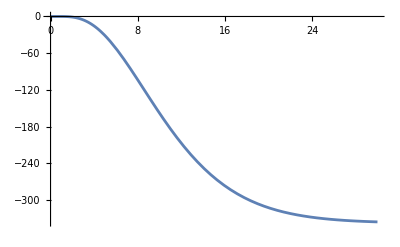

```mathematica
Plot[Subscript[yExp, f][t],{t,0,30},PlotRange->All]
```

```mathematica
Plot[{Subscript[yExp, f][t],Subscript[Y, reg][t],Subscript[Y, tr][t]},{t,0,30},PlotRange->All,PlotLabels->{"Risposta forzata","Risposta a regime","Risposta transitoria"}]
```

-Graphics-

6. Risposta al segnale periodico elementare u (t) = A sin⁡ (ωt + ψ) 1 (t)

```mathematica
Amp := 1
ω := 1
ψ := 0
```

```mathematica
U[t_]:=Amp Sin[ω t+ψ]*UnitStep[t]
```

```mathematica
U[t]
```

Sin[t] UnitStep[t]

```mathematica
U[s_]:=LaplaceTransform[Sin[t]*UnitStep[t],t,s]
```

```mathematica
U[s]
```

1/(1+s^2)

Risposta forzata al segnale periodico considerato

```mathematica
Subscript[Y, f][s]=G[s]U[s]
```

{{(450 (-3+s))/((1+s^2) (2+11 s+15 s^2)^2)}}

```mathematica
yf[s]:=Subscript[D, 1]/(s-ⅈ)+Subscript[D, 2]/(s+ⅈ)+Subscript[D, 31]/(s+2/5)+Subscript[D, 32]/(s+2/5)^2+Subscript[D, 41]/(s+1/3)+Subscript[D, 42]/(s+1/3)^2
```

Per passare al dominio del tempo, scomponiamo in fratti semplici:

```mathematica
Subscript[D, 1]= lim_(s->ⅈ) (s-ⅈ)Subscript[Y, f][s]
```

{{-3645/1682+(1935 ⅈ)/1682}}

```mathematica
Subscript[D, 2]= lim_(s->-ⅈ) (s+ⅈ)Subscript[Y, f][s]
```

{{-3645/1682-(1935 ⅈ)/1682}}

```mathematica
Subscript[D, 2]=Conjugate[Subscript[D, 1]]
```

{{-3645/1682-(1935 ⅈ)/1682}}

```mathematica
Subscript[D, 31]= 1/((2-1)!)lim_(s->-2/5) D[(s+2/5)^2 Subscript[Y, f][s],s]
```

{{-33716250/841}}

```mathematica
Subscript[D, 32]=1/((2-2)!)lim_(s->-2/5) (s+2/5)^2 Subscript[Y, f][s]
```

{{-38250/29}}

```mathematica
Subscript[D, 41]=1/((2-1)!)lim_(s->-1/3) D[(s+1/3)^2 Subscript[Y, f][s],s]
```

{{40095}}

```mathematica
Subscript[D, 42]=1/((2-2)!)lim_(s->-1/3) (s+1/3)^2 Subscript[Y, f][s]
```

{{-1350}}

```mathematica
yf[s]
```

{{-(3645/1682-(1935 ⅈ)/1682)/(-ⅈ+s)-(3645/1682+(1935 ⅈ)/1682)/(ⅈ+s)-1350/(1/3+s)^2+40095/(1/3+s)-38250/(29 (2/5+s)^2)-33716250/(841 (2/5+s))}}

Controlliamo:

```mathematica
Apart[Subscript[Y, f][s]]
```

{{-12150/(1+3 s)^2+120285/(1+3 s)-956250/(29 (2+5 s)^2)-168581250/(841 (2+5 s))-(45 (43+81 s))/(841 (1+s^2))}}

```mathematica
FullSimplify[-(3645/1682-(1935 ⅈ)/1682)/(-ⅈ+s)-(3645/1682+(1935 ⅈ)/1682)/(ⅈ+s)]
```

-(45 (43+81 s))/(841 (1+s^2))

Applichiamo l’antitrasformata ai fattori ottenuti:

```mathematica
yf[t]=InverseLaplaceTransform[yf[s],s,t]
```

{{-33716250/841 ⅇ^(-2 t/5)+40095 ⅇ^(-t/3)-(3645/1682+(1935 ⅈ)/1682) ⅇ^(-ⅈ t)-(3645/1682-(1935 ⅈ)/1682) ⅇ^(ⅈ t)-38250/29 ⅇ^(-2 t/5) t-1350 ⅇ^(-t/3) t}}

```mathematica
Subscript[y, forzata]=yf[t]*UnitStep[t]
```

{{(-33716250/841 ⅇ^(-2 t/5)+40095 ⅇ^(-t/3)-(3645/1682+(1935 ⅈ)/1682) ⅇ^(-ⅈ t)-(3645/1682-(1935 ⅈ)/1682) ⅇ^(ⅈ t)-38250/29 ⅇ^(-2 t/5) t-1350 ⅇ^(-t/3) t) UnitStep[t]}}

Suddividiamo la risposta forzata in risposta a regime e risposta transitoria

```mathematica
Subscript[y, regime][t_]:=ComplexExpand[Re[2 Subscript[D, 1] ⅇ^(ⅈ*t)]]
```

```mathematica
Subscript[y, regime][t]
```

{{-(3645 Cos[t])/841-(1935 Sin[t])/841}}

```mathematica
Simplify[Subscript[y, regime][t]]
```

{{-45/841 (81 Cos[t]+43 Sin[t])}}

```mathematica
Subscript[y, transitoria][t_]:=-(33716250 ⅇ^(-2t/5))/841+40095 ⅇ^(-t/3)-(38250 ⅇ^(-2 t/5))/29 t-1350 ⅇ^(-t/3) t
```

```mathematica
Subscript[y, transitoria][t]
```

-33716250/841 ⅇ^(-2 t/5)+40095 ⅇ^(-t/3)-38250/29 ⅇ^(-2 t/5) t-1350 ⅇ^(-t/3) t

Grafici

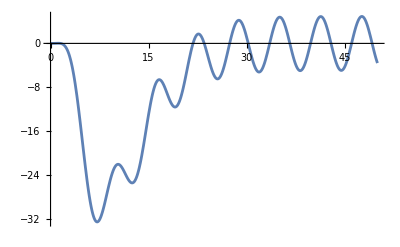

```mathematica
Plot[Subscript[y, forzata],{t,0,50},PlotRange->All]
```

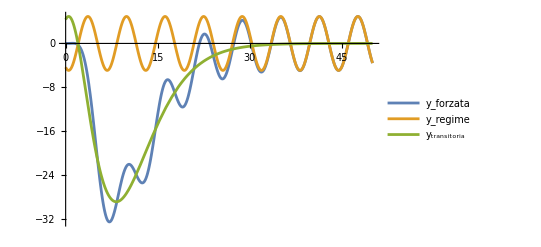

```mathematica
Plot[{Subscript[y, forzata],Subscript[y, regime][t],Subscript[y, transitoria][t]},{t,0,50},PlotRange->All,PlotLegends->{"y_forzata","y_regime","y_transitoria"}]
```

Procediamo determinando la coppia ampiezza - fase della risposta a regime. Valutiamo le seguenti due equazioni in t = 0.

-(3645 cos(t))/841-(1935 sin(t))/841=A sin(t+ψ)

d/dt(-(3645 cos(t))/841-(1935 sin(t))/841)=d/dt(A sin(t+ψ))

```mathematica
Subscript[y, regime][t]
```

{{-(3645 Cos[t])/841-(1935 Sin[t])/841}}

```mathematica
Solve[{(Subscript[y, regime][t]==X Sin[t+θ])/.{t->0},(D[Subscript[y, regime][t],t]==D[X Sin[t+θ],t])/.{t->0},X>0},{X,θ}]
```

{{X→ConditionalExpression[(45 √10)/29, C[1]∈ℤ],θ→ConditionalExpression[-2 ArcTan[(290+43 √10)/(81 √10)]+2 π C[1], C[1]∈ℤ]}}

Valori trovati di ampiezza e fase:

```mathematica
ampiezza = N[(45 √10)/29]
```

4.90698

```mathematica
fase=N[-2 ArcTan[(290+43 √10)/(81 √10)]](180/π)
```

-117.962

7. Modello ARMA

```mathematica
Factor[G[s][[1,1]]]
```

(450 (-3+s))/((1+3 s)^2 (2+5 s)^2)

```mathematica
Expand[(2+5s)^2(1+3s)^2]
```

4+44 s+181 s^2+330 s^3+225 s^4

```mathematica
Subscript[x, 0]={{0},{-1},{3},{-1}}
```

{{0},{-1},{3},{-1}}

```mathematica
Subscript[x, 0]//MatrixForm
```

(0
-1
3
-1)

```mathematica
equDiff=225y''''[t]+330y'''[t]+181y''[t]+44y'[t]+4y[t]==450u'[t]-1350u[t]
```

4 y[t]+44 y'[t]+181 y''[t]+330 y^(3)[t]+225 y^(4)[t]==-1350 u[t]+450 u'[t]

```mathematica
Lp = LaplaceTransform[equDiff,t,s]
```

4 LaplaceTransform[y[t],t,s]+44 (s LaplaceTransform[y[t],t,s]-y[0])+181 (s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0])+330 (s^3 LaplaceTransform[y[t],t,s]-s^2 y[0]-s y'[0]-y''[0])+225 (s^4 LaplaceTransform[y[t],t,s]-s^3 y[0]-s^2 y'[0]-s y''[0]-y^(3)[0])==-1350 LaplaceTransform[u[t],t,s]+450 (s LaplaceTransform[u[t],t,s]-u[0])

```mathematica
y[0]=(C1.Subscript[x, 0])[[1,1]]
y'[0]=(C1.A.Subscript[x, 0])[[1,1]]
y''[0]=(C1.A.A.Subscript[x, 0])[[1,1]]
y'''[0]=(C1.A.A.A.Subscript[x, 0])[[1,1]]
```

-26

-4

32

-16/25

```mathematica
newEq = 4Y[s]+44(-y[0]+s Y[s])+181(-s y[0]+s^2 Y[s]-y'[0])+330[-s^2 y[0]+s^3 Y[s]-s y'[0]-y''[0]]+225(-s^3 y[0]+s^4 Y[s]-s^2 y'[0]-s y''[0]-y'''[0])== -1350U[s]+450s U[s]
```

330[-32+4 s+26 s^2+s^3 Y[s]]+4 Y[s]+44 (26+s Y[s])+181 (4+26 s+s^2 Y[s])+225 (16/25-32 s+4 s^2+26 s^3+s^4 Y[s])==-1350 U[s]+450 s U[s]

Inseriamo la risposta libera

```mathematica
Subscript[Y, lib][s_]:=(8548+1174s-9480 s^2-5850 s^3)/(4+44s+181 s^2+330 s^3+225 s^4)
```

```mathematica
Factor[Subscript[Y, lib][s]]
```

-(2 (-4274-587 s+4740 s^2+2925 s^3))/((1+3 s)^2 (2+5 s)^2)

Applichiamo il metodo dei fratti semplici

```mathematica
Subscript[L, 11](1/(s+1/3))+Subscript[L, 12](1/(s+1/3)^2)+Subscript[L, 21](1/(s+2/5))+Subscript[L, 22](1/(s+2/5)^2)
```

L_11/(1/3+s)+L_12/(1/3+s)^2+L_21/(2/5+s)+L_22/(2/5+s)^2

```mathematica
Subscript[L, 12]=lim_(s->-1/3) (s+1/3)^2 Subscript[Y, lib][s]
```

7320

```mathematica
Subscript[L, 11]=lim_(s->-1/3) D[(s+1/3)^2 Subscript[Y, lib][s],s]
```

-214056

```mathematica
Subscript[L, 22]=lim_(s->-2/5) (s+2/5)^2 Subscript[Y, lib][s]
```

6936

```mathematica
Subscript[L, 21]=lim_(s->-2/5) D[(s+2/5)^2 Subscript[Y, lib][s],s]
```

214030

```mathematica
Subscript[L, 11](1/(s+1/3))+Subscript[L, 12](1/(s+1/3)^2)+Subscript[L, 21](1/(s+2/5))+Subscript[L, 22](1/(s+2/5)^2)
```

7320/(1/3+s)^2-214056/(1/3+s)+6936/(2/5+s)^2+214030/(2/5+s)

Dominio del tempo

```mathematica
Subscript[Y, libt][t_]:=Subscript[L, 11] Exp[-1/3 t]UnitStep[t]+Subscript[L, 12] t Exp[-1/3 t]UnitStep[t]+Subscript[L, 21] Exp[-2/5 t]UnitStep[t]+Subscript[L, 22] t Exp[-2/5 t]UnitStep[t]
```

```mathematica
Subscript[Y, libt][t]
```

214030 ⅇ^(-2 t/5) UnitStep[t]-214056 ⅇ^(-t/3) UnitStep[t]+6936 ⅇ^(-2 t/5) t UnitStep[t]+7320 ⅇ^(-t/3) t UnitStep[t]

Accertiamoci della correttezza dei calcoli, utilizzando la funzione InverseLaplaceTrasform

```mathematica
Expand[InverseLaplaceTransform[Subscript[Y, lib][s],s,t]]
```

214030 ⅇ^(-2 t/5)-214056 ⅇ^(-t/3)+6936 ⅇ^(-2 t/5) t+7320 ⅇ^(-t/3) t

Calcoliamo la risposta alla rampa unitaria

```mathematica
Subscript[U, rampa][s_]= LaplaceTransform[Piecewise[{{t,t>=0},{0,t<0}}],t,s]
```

1/s^2

```mathematica
G [s][[1,1]]
```

(450 (-3+s))/((2+11 s+15 s^2)^2)

```mathematica
Subscript[y, rampa][s_]:=G[s][[1,1]] 1/s^2
```

```mathematica
Factor[Subscript[y, rampa][s]]
```

(450 (-3+s))/(s^2 (1+3 s)^2 (2+5 s)^2)

Utilizziamo il metodo dei fratti semplici per calcolare l’antitrasformata di Laplace

```mathematica
Subscript[R, 11](1/s)+Subscript[R, 12](1/s^2)+Subscript[R, 21](1/(s+1/3))+Subscript[R, 22](1/(s+1/3)^2)+Subscript[R, 31](1/(s+2/5))+Subscript[R, 32](1/(s+2/5)^2)
```

R_11/s+R_12/s^2+R_21/(1/3+s)+R_22/(1/3+s)^2+R_31/(2/5+s)+R_32/(2/5+s)^2

```mathematica
Subscript[R, 22]=lim_(s->-1/3) (s+1/3)^2 Subscript[y, rampa][s]
```

-13500

```mathematica
Subscript[R, 21]=lim_(s->-1/3) D[(s+1/3)^2 Subscript[y, rampa][s],s]
```

328050

```mathematica
Subscript[R, 32]=lim_(s->-2/5) (s+2/5)^2 Subscript[y, rampa][s]
```

-19125/2

```mathematica
Subscript[R, 31]=lim_(s->-2/5) D[(s+2/5)^2 Subscript[y, rampa][s],s]
```

-331875

```mathematica
Subscript[R, 12]=lim_(s->0) s^2 Subscript[y, rampa][s]
```

-675/2

```mathematica
Subscript[R, 11]=lim_(s->0) D[s^2 Subscript[y, rampa][s],s]
```

3825

Controlliamo se i calcoli sono giusti tramite la funzione Apart

```mathematica
Apart[Subscript[y, rampa][s]]
```

-675/(2 s^2)+3825/s-121500/(1+3 s)^2+984150/(1+3 s)-478125/(2 (2+5 s)^2)-1659375/(2+5 s)

```mathematica
Subscript[R, 11](1/s)+Subscript[R, 12](1/s^2)+Subscript[R, 21](1/(s+1/3))+Subscript[R, 22](1/(s+1/3)^2)+Subscript[R, 31](1/(s+2/5))+Subscript[R, 32](1/(s+2/5)^2)
```

-675/(2 s^2)+3825/s-13500/(1/3+s)^2+328050/(1/3+s)-19125/(2 (2/5+s)^2)-331875/(2/5+s)

```mathematica
Subscript[yt, rampa][t_]:=Subscript[R, 11] UnitStep[t]+Subscript[R, 12] t UnitStep[t]+Subscript[R, 21] Exp[-1/3 t]UnitStep[t]+Subscript[R, 22] t Exp[-1/3 t]UnitStep[t]+Subscript[R, 31] Exp[-2/5 t]UnitStep[t]+Subscript[R, 32] t Exp[-2/5 t]UnitStep[t]
```

```mathematica
Expand[Subscript[yt, rampa][t]]
```

3825 UnitStep[t]-331875 ⅇ^(-2 t/5) UnitStep[t]+328050 ⅇ^(-t/3) UnitStep[t]-675/2 t UnitStep[t]-19125/2 ⅇ^(-2 t/5) t UnitStep[t]-13500 ⅇ^(-t/3) t UnitStep[t]

Confrontiamo il risultato ottenuto con quello della funzione InverseLaplaceTrasform:

```mathematica
Expand[InverseLaplaceTransform[Subscript[y, rampa][s],s,t]]
```

3825-331875 ⅇ^(-2 t/5)+328050 ⅇ^(-t/3)-(675 t)/2-19125/2 ⅇ^(-2 t/5) t-13500 ⅇ^(-t/3) t

Individuiamo risposta a regime e risposta transitoria:

```mathematica
Subscript[yr, regime][t]=3825-(675 t)/2
```

3825-(675 t)/2

```mathematica
Subscript[yr, transitoria][t]=31875 ⅇ^(-2 t/5)+328050 ⅇ^(-t/3)-19125/2 ⅇ^(-2 t/5) t-13500 ⅇ^(-t/3) t
```

31875 ⅇ^(-2 t/5)+328050 ⅇ^(-t/3)-19125/2 ⅇ^(-2 t/5) t-13500 ⅇ^(-t/3) t

Infine, la risposta totale sarà:

```mathematica
Subscript[Y, libt][t]
```

214030 ⅇ^(-2 t/5) UnitStep[t]-214056 ⅇ^(-t/3) UnitStep[t]+6936 ⅇ^(-2 t/5) t UnitStep[t]+7320 ⅇ^(-t/3) t UnitStep[t]

```mathematica
Subscript[yt, rampa][t]
```

3825 UnitStep[t]-331875 ⅇ^(-2 t/5) UnitStep[t]+328050 ⅇ^(-t/3) UnitStep[t]-675/2 t UnitStep[t]-19125/2 ⅇ^(-2 t/5) t UnitStep[t]-13500 ⅇ^(-t/3) t UnitStep[t]

```mathematica
Subscript[yr, tot][t_]:= Subscript[Y, libt][t]+Subscript[yt, rampa][t]
```

```mathematica
Subscript[yr, tot][t]
```

3825 UnitStep[t]-117845 ⅇ^(-2 t/5) UnitStep[t]+113994 ⅇ^(-t/3) UnitStep[t]-675/2 t UnitStep[t]-5253/2 ⅇ^(-2 t/5) t UnitStep[t]-6180 ⅇ^(-t/3) t UnitStep[t]

8. Stato iniziale x0 tale che la risposta al gradino coincida con il suo valore di regime

Riprendiamo la FdT

```mathematica
G[s][[1,1]]
```

(450 (-3+s))/((2+11 s+15 s^2)^2)

Scriviamo il vettore di stato iniziale, le cui componenti sono al momento incognite

```mathematica
x0 = {{x1},{x2},{x3},{x4}}
```

{{x1},{x2},{x3},{x4}}

```mathematica
Subscript[risp, lib]=Simplify[C1.Inverse[s IdentityMatrix[4]-A].x0][[1,1]]
```

(2 ((-1533-1154 s-120 s^2+225 s^3) x1+(-1397-611 s+870 s^2+900 s^3) x2+854 x3-198 s x3-1215 s^2 x3-675 s^3 x3-315 x4-570 s x4+225 s^2 x4))/(2+11 s+15 s^2)^2

```mathematica
Subscript[risp, forz]=Simplify[G[s](1/s)][[1,1]]
```

(450 (-3+s))/(s (2+11 s+15 s^2)^2)

```mathematica
Subscript[risp, reg]=(G[0](1/s))[[1,1]]
```

-675/(2 s)

```mathematica
Subscript[risp, tran]=Factor[Subscript[risp, forz]-Subscript[risp, reg]]
```

(225 (136+543 s+990 s^2+675 s^3))/(2 (1+3 s)^2 (2+5 s)^2)

```mathematica
Numerator[Simplify[Expand[Subscript[risp, lib]+Subscript[risp, tran]]]]
```

225 s^3 (675+4 x1+16 x2-12 x3)-30 s^2 (-7425+16 x1-116 x2+162 x3-30 x4)-4 (-7650+1533 x1+1397 x2-854 x3+315 x4)-s (-122175+4616 x1+2444 x2+792 x3+2280 x4)

```mathematica
CF = CoefficientList[Numerator[Simplify[Expand[Subscript[risp, lib]+Subscript[risp, tran]]]],s]
```

{-4 (-7650+1533 x1+1397 x2-854 x3+315 x4),122175-4616 x1-2444 x2-792 x3-2280 x4,-30 (-7425+16 x1-116 x2+162 x3-30 x4),225 (675+4 x1+16 x2-12 x3)}

Li eguagliamo a 0 per trovare le componenti di x0

```mathematica
Solve[CF == {0,0,0,0},{x1,x2,x3,x4}]
```

{{x1→225/4,x2→-225/4,x3→0,x4→0}}

Controlliamo se, a partire da questo stato iniziale, viene effettivamente generata solo la risposta a regime

```mathematica
Σ
```

04/22559/75-76/22511221/225-134/75301/225-12446/225-134/75301/225-11221/225-59/75-149/225-128-600StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1141FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Subscript[risp, reg]
```

-675/(2 s)

```mathematica
OutputResponse[{Σ,{225/4,-225/4,0,0}},1,t]
```

{-675/2}

9. Risposta al segnale u(t) = 1 (-t)

Risposta a regime

```mathematica
G[s][[1,1]]
```

(450 (-3+s))/((2+11 s+15 s^2)^2)

```mathematica
yreg = G[0][[1,1]]
```

-675/2

Matrice di osservabilità

```mathematica
θ = {C1[[1]],(C1.A)[[1]],(C1.A.A)[[1]],(C1.A.A.A)[[1]]}
```

{{2,8,-6,0},{-4,-4,-2,2},{-6,-6,6,-8},{-2,-442/225,118/75,1648/225}}

```mathematica
Det[θ]
```

18496/9

Stato iniziale

```mathematica
statoI = Inverse[θ].{{G[0][[1,1]]},{0},{0},{0}}
```

{{16173/289},{-3807/68},{297/1156},{243/1156}}

Risposta libera, calcolata mediante la sua definizione

```mathematica
yliberas = Simplify[(C1.Inverse[s IdentityMatrix[4]-A].statoI)[[1,1]]]
```

-(675 (44+181 s+330 s^2+225 s^3))/(2 (2+11 s+15 s^2)^2)

Visualizziamola tramite fratti semplici

```mathematica
Apart[yliberas]
```

-36450/(1+3 s)^2+328050/(1+3 s)-84375/(2+5 s)^2-1096875/(2 (2+5 s))

Antitrasformiamo, per ottenere la risposta libera nel dominio del tempo

```mathematica
yliberat[t_]:=InverseLaplaceTransform[yliberas,s,t]
```

```mathematica
yliberat[t]
```

-675/2 (12 ⅇ^(-t/3) (-27+t)+5 ⅇ^(-2 t/5) (65+2 t))

Uniamo le due componenti trovate

```mathematica
Subscript[y, g][t_] := Piecewise[{{yreg, t<0}, {yliberat[t], t>=0}}]
```

Grafico

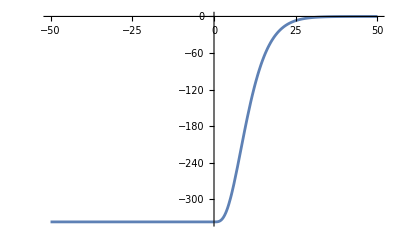

```mathematica
Plot[Subscript[y, g][t],{t,-50,50},PlotRange->All]
```